Lawrence Lee

北京理工大学

2020.10.31

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

```mathematica
<<MaTeX`
```

可能用到的表达式

```mathematica
ToExpression["\\sqrt{\\frac{x}{y}}",TeXForm]
```

√(x/y)

提高MMA运算速度

["10 Tips for Writing Fast Mathematica Code"](https://blog.wolfram.com/2011/12/07/10-tips-for-writing-fast-mathematica-code/)

["Performance tuning in Mathematica?"](https://mathematica.stackexchange.com/questions/29349/performance-tuning-in-mathematica)

一些MMA中找不到对应的符号的LaTeX的写法

```mathematica
MaTeX["\\propto",Magnification->2]
```

-Graphics-

或直接用妈咪叔的网站找

LaTeX公式编辑器www.latexlive.comNonewww.latexlive.com

## ￿1 6 .5 规范场与玻色场耦合体系

#### 为何说拓扑荷=磁荷？

徐：电荷如何计算？

对*J进行体积分=对(d^*F)/(4π)进行体积分（麦氏方程）=对*F进行面积分（斯托克斯定理）

*F在空间超曲面上的限制=*E

由于是在空间超曲面上的曲面进行积分，所以*F可以放心替换为*E，于是区域内电荷量就=在边界上对*E进行积分

这里类比电荷的产生，把他叫做磁荷

#### 为何到磁荷F就成了李代数数值的二形式

电磁场规范群是U(1)只有一维，故李代数只有一个分量，就只需要实的2-形式了。

#### 矢量丛的秩？

矢量从的典型纤维的维数

#### 典型纤维

-Graphics-

注：伴矢丛的典型纤维是矢量空间

#### 为何说拓扑荷=磁荷？

F_jk^a为SU(2)规范场的规范场强【李代数数值的微分二形式】

H_i^a==1/2 ϵ_ijk F_jk^a为SU(2)规范场的磁场

规范场与波色场耦合时，若…（条件复杂，省略），则存在涡旋.
类比电荷的计算方式，拓扑示性数【=复线丛L的第1陈数=涡旋数】的计算公式如下

```mathematica
∫d^3 x D[(Subscript[H, a]^i ϕ^a), i]==n
```

该值是由无穷远边界条件决定的、且规范不变的、整数、守恒荷，为拓扑荷。

由于H_i^a为SU(2)规范场的磁场，故拓扑荷也叫磁荷【只是个数学上的类比，而非普通意义上的磁场由磁荷引起】。

补充：复线丛L的第1陈数c_1

```mathematica
Subscript[c, 1]==i/(2π)∫F
```

#### 李群哥补充

阿贝尔规范场中，磁场的散度为0，磁单极子在非阿贝尔场规范场中有。

非阿贝尔规范场中有磁荷，电磁场的规范群是U(1)，并不存在磁荷。

非阿贝尔规范场的方程跟麦克斯韦比较后感觉有磁荷,并不是说普通意义上的磁场是磁荷引起的，只是个数学上的类比

电荷产生电场
磁荷产生磁场

#### 徐

电磁场里也可以有磁荷，只需要先对称化麦氏方程(不改变实质)，然后你就会发现电磁场潜在的另一个规范自由性【电场和磁场可以进行一个整体SO(2)”旋转”规范而不改变物理实质】。
作一个规范变换后电子等粒子也就有磁荷了，但是磁单极子仍然不存在啊，不需要存在，这个规范变换叫电磁场的对偶变换。

实质问题是电荷磁荷之比，目前发现的粒子都测得具有近乎相同的电荷磁荷比，因此总可以找到一个规范使得只存在电荷而无磁荷，但是如果忽略这条
，不指定规范，那么磁荷是可以存在的。

#### 证明：磁荷的存在性=磁单极子的存在性

磁荷可以选定规范而存在 或 不存在，磁单极子的存在性与规范选取无关。

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[-Graphics-,RasterSize->600]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 2.

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->600]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 3.

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->600]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 4.

#### 工具

```mathematica
Hyperlink["",""]//Print
```

```mathematica
Rasterize[,RasterSize->600]//Print
```

```mathematica
HoldForm[]//MaTeX[#,Magnification->2]&//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

```mathematica
(%//AbsoluteTiming)⟦1⟧*1000
```

## 技巧

### 1. Flatten

-Graphics-

用TreeForm辅助，看应该把哪两层放在一起

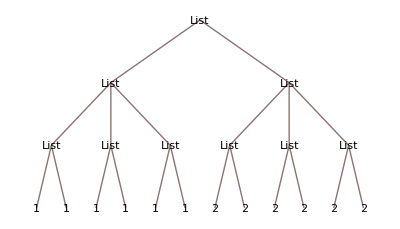

{{1,1,1},{2,2,2}}

0.0027

```mathematica
{{{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2}}}//TreeForm
Flatten[{{{1},{1},{1}},{{2},{2},{2}}},{{1},{2,3}}]
a=(%//AbsoluteTiming)⟦1⟧*1000
```

```mathematica
Flatten[{{1},{1},{1}},2]
Flatten[#,2]&/@{{{1,1},{1,1},{1,1}},{{2,2},{2,2},{2,2}}}
b=(%//AbsoluteTiming)⟦1⟧*1000
```

{1,1,1}

{{1,1,1,1,1,1},{2,2,2,2,2,2}}

0.0023